### randomly choose a real, symmetric matrix

```mathematica
e0=22;
dim =24;
Ham=Table[N[i j/(i^2+j+1)],{i,dim},{j,dim}];
LITham[hh_,nn_,σr_,σi_,B0_]:=Eigenvalues[hh-(B0+σr+I σi) nn][[1]]
srtest=10;
sitest=0.5;
LITham[Ham,IdentityMatrix[dim],srtest,sitest,e0]
```

-32.-0.5 ⅈ

```mathematica
Plot3D[Re[LITham[Ham,IdentityMatrix[dim],sr,si,e0][[1]]],{sr,0,200},{si,0.1,5},PlotPoints->90]
```

-Graphics3D-

~/kette_repo/ComptonLIT/av18_deuteron/norm-ham-litME-0-

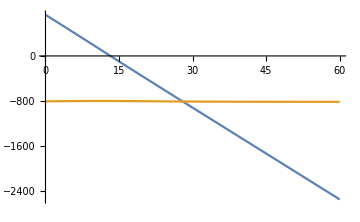
-Graphics- | -Graphics3D-E_0 = -1.8 MeV

```mathematica
MUL=1;
jj =0;
mJ=0;
pi="-";
file="~/kette_repo/ComptonLIT/av18_deuteron/norm-ham-litME-"<>ToString[jj]<>pi
NormHamMat=ReadList[file,Number];
JbasisDim=NormHamMat[[1]];
norm=ArrayReshape[NormHamMat[[2;;JbasisDim^2+1]],{JbasisDim,JbasisDim}];ham=ArrayReshape[NormHamMat[[JbasisDim^2+2;;2 JbasisDim^2+1]],{JbasisDim,JbasisDim}];
Ed=-1.8;σi=15;
Labeled[
Grid[{{
Plot[{Re[LITham[ham,norm,σr,σi,Ed]],Im[LITham[ham,norm,σr,σi,Ed]]},{σr,0,60},
ImageSize->Medium],
Plot3D[Re[LITham[ham,norm,σr,σi,Ed]],{σr,10,20},{σi,0,1},AxesLabel->{"σ_r","σ_i"},PlotPoints->910,
ImageSize->Medium]
}}
],{"E_0 = "<>ToString[Ed]<>" MeV"},{Top}]
```